```mathematica
OS="win";(*or,linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
Needs["CustomTicks`"];
SetOptions[LinTicks,TickLabelStep->1,MajorTickLength->{0.0125,0},MinorTickLength->{0.0075,0}];
If[OS=="win",
Print["Working Directory: ",descDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\analysis-mirror_neutrons\\nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\rawdata"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["C:\\Users\\tmpra\\Dropbox\\Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\Pictures\\nstar\\runs2"];Print["(SysDir) System Directory: ",SysDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="\\";
];
If[OS=="axion",
Print["Working Directory: ",descDir="/home/prajwal/Dropbox/nEDM/analysis-mirror_neutrons/nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="/home/prajwal/Dropbox/nEDM/rawdata"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["/home/prajwal/Dropbox/Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="/home/prajwal/Dropbox/nEDM/Pictures/nstar/runs"];Print["(SysDir) System Directory: ",SysDir="/home/prajwal/Dropbox/nEDM/system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="/";
];
metaStructure={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
metadesc={Number,Number,Number,Number,Number,Number,Number,Word,Real,Real,Real,Real};
descdat=ReadList[StringJoin[descDir,seperator,"desctf_c.dat"],metadesc];
dimdesc=Dimensions[descdat][[1]];
metalvl3={Real,Real,Real,Real,Real,Real,Real,Real};
metalvl2={Real,Real,Real,Real,Real,Real,Real,Real,Real};
```

Working Directory: C:\Users\tmpra\Dropbox\nEDM\analysis-mirror_neutrons\nstar_online

(AscDir) Rawdata Directory: C:\Users\tmpra\Dropbox\nEDM\rawdata

(ScrDir) Scratch Directory: C:\Users\tmpra\Dropbox\Scratch

(PicDir) Picture Directory: C:\Users\tmpra\Dropbox\nEDM\Pictures\nstar\runs2

(SysDir) System Directory: C:\Users\tmpra\Dropbox\nEDM\system

Rawdata on mpc1636:/xdata/nedm_data/RawData

## E

Run 10 #: 12693

Run 10 #: 12695

Run 10 #: 12697

Run 10 #: 12704

Run 10 #: 12707

Run 10 #: 12771

Run 10 #: 12775

Run 10 #: 12778

Run 10 #: 12779

Run 10 #: 12780

Run 20 #: 13102

Run 20 #: 13104

Run 20 #: 13106

Run 20 #: 13107

Part::partw: Part 1 of {} does not exist.

Part::partw: Part -1 of {} does not exist.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Run 20 #: 13133

Run 20 #: 13138

Run 20 #: 13142

Run 20 #: 13146

| Estimate | Standard Error | t-Statistic | P-Value
m | 0.000391404 | 0.000339264 | 1.15369 | 0.28193
c | -0.0182153 | 0.0888642 | -0.204979 | 0.842708

| DF | SS | MS
Model | 2 | 0.00317342 | 0.00158671
Error | 8 | 0.00279388 | 0.000349235
Uncorrected Total | 10 | 0.00596729 | 
Corrected Total | 9 | 0.00325871 |

1.00035

χ2_10: 1.2654

| Estimate | Standard Error | t-Statistic | P-Value
m | 0.0000385802 | 0.00037594 | 0.102623 | 0.921606
c | -0.103659 | 0.283559 | -0.365562 | 0.727233

| DF | SS | MS
Model | 2 | 0.00270007 | 0.00135004
Error | 6 | 0.0216628 | 0.00361047
Uncorrected Total | 8 | 0.0243629 | 
Corrected Total | 7 | 0.0217009 |

1.00361

χ2_20: 1.07472

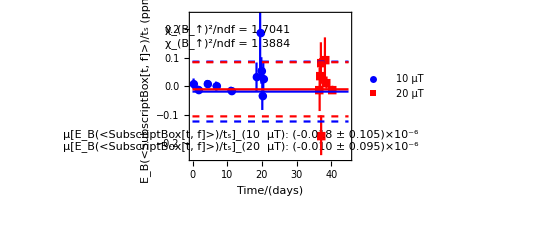

```mathematica
lvl3={};
lvl2={};
tsadd=PlusMinus[11.306,0.397];
sttime=0;
pttstfe10={};fttstfe10={};errtstfe10={};
pttstfet10={};fttstfet10={};errtstfet10={};
pttstfe20={};fttstfe20={};errtstfe20={};
pttstfet20={};fttstfet20={};errtstfet20={};
For[i=1,i≤dimdesc,i++,
lvl2=ReadList[StringJoin[AscDir,seperator,IntegerString[descdat[[i]][[4]],10,6],seperator,IntegerString[descdat[[i]][[4]],10,6],"_lvl2.dat"],metalvl2];
If[i==1,sttime=lvl2[[1]][[1]]];
xx=((Abs[-lvl2[[1]][[1]]+lvl2[[-1]][[1]]]/2)+Abs[lvl2[[1]][[1]]-sttime])/(24*3600);
If[(!MemberQ[{6,8,9,10,15,17,21,22,23,24,25,27,28,29,30,32,33,37},i]&&descdat[[i]][[6]]==10)
,
Print["Run 10 #: ",descdat[[i]][[4]]];
lvl3=ReadList[StringJoin[AscDir,seperator,IntegerString[descdat[[i]][[4]],10,6],seperator,IntegerString[descdat[[i]][[4]],10,6],"_lvl3.dat"],metalvl3];
ts=(PlusMinus[descdat[[i]][[7]],.1]+tsadd)/PlusMinus[descdat[[i]][[9]],descdat[[i]][[10]]];
(***)
pttstfe10=AppendTo[pttstfe10,{{ts[[1]],ts[[2]]},{lvl3[[1]][[3]],lvl3[[1]][[4]]}*(descdat[[i]][[9]]*10^6/ts[[1]])}];
fttstfe10=AppendTo[fttstfe10,{ts[[1]],lvl3[[1]][[3]]}*(descdat[[i]][[9]]*10^6/ts[[1]])];
errtstfe10=AppendTo[errtstfe10,Sqrt[ts[[2]]^2+lvl3[[1]][[4]]^2]*(descdat[[i]][[9]]*10^6/ts[[1]])];
(***)
pttstfet10=AppendTo[pttstfet10,{xx,{lvl3[[1]][[3]],lvl3[[1]][[4]]}*(descdat[[i]][[9]]*10^6/ts[[1]])}];
fttstfet10=AppendTo[fttstfet10,{xx,lvl3[[1]][[3]]}*(descdat[[i]][[9]]*10^6/ts[[1]])];
errtstfet10=AppendTo[errtstfet10,lvl3[[1]][[4]]*(descdat[[i]][[9]]*10^6/ts[[1]])];
];
If[(!MemberQ[{6,8,9,10,15,17,21,22,23,24,25,27,28,29,30,32,33,34,37},i]&&descdat[[i]][[6]]==20)
,
Print["Run 20 #: ",descdat[[i]][[4]]];
lvl3=ReadList[StringJoin[AscDir,seperator,IntegerString[descdat[[i]][[4]],10,6],seperator,IntegerString[descdat[[i]][[4]],10,6],"_lvl3.dat"],metalvl3];
ts=(PlusMinus[descdat[[i]][[7]],.1]+tsadd)/PlusMinus[descdat[[i]][[9]],descdat[[i]][[10]]];
(***)
pttstfe20=AppendTo[pttstfe20,{{ts[[1]],ts[[2]]},{lvl3[[1]][[3]],lvl3[[1]][[4]]}*(descdat[[i]][[9]]*10^6/ts[[1]])}];
fttstfe20=AppendTo[fttstfe20,{ts[[1]],lvl3[[1]][[3]]}*(descdat[[i]][[9]]*10^6/ts[[1]])];
errtstfe20=AppendTo[errtstfe20,Sqrt[ts[[2]]^2+lvl3[[1]][[4]]^2]*(descdat[[i]][[9]]*10^6/ts[[1]])];
(***)
pttstfet20=AppendTo[pttstfet20,{xx,{lvl3[[1]][[3]],lvl3[[1]][[4]]}*(descdat[[i]][[9]]*10^6/ts[[1]])}];
fttstfet20=AppendTo[fttstfet20,{xx,lvl3[[1]][[3]]}*(descdat[[i]][[9]]*10^6/ts[[1]])];
errtstfet20=AppendTo[errtstfet20,lvl3[[1]][[4]]*(descdat[[i]][[9]]*10^6/ts[[1]])];
];
]
nlm10=NonlinearModelFit[fttstfet10,m x + c,{m,c},x,Weights->errtstfet10];
ftval10={m/.nlm10["BestFitParameters"],c/.nlm10["BestFitParameters"]};
fterr10=nlm10["ParameterErrors"];
ftresidue10=nlm10["FitResiduals"];
nlm10["ParameterTable"]
nlm10["ANOVATable"]
1+nlm10["EstimatedVariance"]
ndim10=Dimensions[fttstfet10][[1]];
Print["χ2_10: ",(√(∑_(i=1)^ndim10 (pttstfet10[[i]][[2]][[1]]/pttstfet10[[i]][[2]][[2]])^2))/ndim10+1]
(*20*)
nlm20=NonlinearModelFit[fttstfet20,m x + c,{m,c},x,Weights->errtstfet20];
ftval20={m/.nlm20["BestFitParameters"],c/.nlm20["BestFitParameters"]};
fterr20=nlm20["ParameterErrors"];
ftresidue20=nlm20["FitResiduals"];
nlm20["ParameterTable"]
nlm20["ANOVATable"]
1+nlm20["EstimatedVariance"]
ndim20=Dimensions[fttstfet20][[1]];
Print["χ2_20: ",(√(∑_(i=1)^ndim20 (pttstfet20[[i]][[2]][[1]]/pttstfet20[[i]][[2]][[2]])^2))/ndim20]
Show[{
EDAListPlot[pttstfet10,pttstfet20,PlotRange->{{-.05,45},{-.25,.25}},PlotLegends->{"10 μT","20 μT"},Frame->True,FrameLabel->{"Time/(days)","E_B(<SubscriptBox[t, f]>)/t_s (ppm)"},PlotStyle->{Blue,Red},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->36],LabelStyle->{36,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->{1000},
Epilog->{
Text[Style["χ_(B_↑)^2/ndf = 1.3884",FontSize->Large],{10,.15}],
Text[Style["χ_(B_↑)^2/ndf = 1.7041",FontSize->Large],{10,.2}],
Text[Style["μ[E_B(<SubscriptBox[t, f]>)/t_s]_(10  μT): (-0.018 ± 0.105)×10^-6\nμ[E_B(<SubscriptBox[t, f]>)/t_s]_(20  μT): (-0.010 ± 0.095)×10^-6",FontSize->Large],{14,-.19}]
},PlotMarkers->{Automatic,Medium}
],
EDAListPlot[pttstfet10,pttstfet20,PlotRange->{{-.05,45},{-.0245,.0245}},Frame->True,FrameLabel->{"Time/(days)","E_B(<SubscriptBox[t, f]>)/t_s (ppm)"},FrameTicks->LinTicks,PlotStyle->{Blue,Red},TicksStyle->Directive[FontSize->36],LabelStyle->{36,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->{1000}
],
Plot[{-0.018,-0.018+0.105,-0.018-0.105,-0.010,-0.010+0.095,-0.010-0.095},{x,-.05,45},PlotStyle->{Blue,{Dashed,Blue},{Dashed,Blue},Red,{Dashed,Red},{Dashed,Red}}]
}]
```

## A

Part::partw: Part 1 of {} does not exist.

Part::partw: Part -1 of {} does not exist.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

| Estimate | Standard Error | t-Statistic | P-Value
m | -0.000141904 | 0.000210155 | -0.675236 | 0.516496
c | 0.00821916 | 0.0550073 | 0.149419 | 0.884517

| DF | SS | MS
Model | 2 | 0.000270103 | 0.000135052
Error | 9 | 0.000862309 | 0.0000958121
Uncorrected Total | 11 | 0.00113241 | 
Corrected Total | 10 | 0.000905994 |

1.0001

χ2_10: 1.36247

| Estimate | Standard Error | t-Statistic | P-Value
m | -0.0000334701 | 0.000132217 | -0.253145 | 0.804115
c | -0.041077 | 0.129337 | -0.317597 | 0.755834

| DF | SS | MS
Model | 2 | 0.00360884 | 0.00180442
Error | 13 | 0.0186886 | 0.00143758
Uncorrected Total | 15 | 0.0222974 | 
Corrected Total | 14 | 0.0187807 |

1.00144

χ2_20: 0.704134

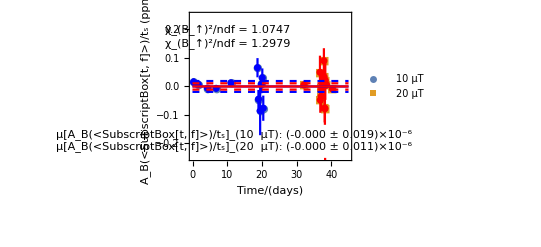

```mathematica
lvl3={};
lvl2={};
tsadd=PlusMinus[11.306,0.397];
sttime=0;
pttstfe10={};fttstfe10={};errtstfe10={};
pttstfet10={};fttstfet10={};errtstfet10={};
pttstfe20={};fttstfe20={};errtstfe20={};
pttstfet20={};fttstfet20={};errtstfet20={};
For[i=1,i≤dimdesc,i++,
lvl2=ReadList[StringJoin[AscDir,seperator,IntegerString[descdat[[i]][[4]],10,6],seperator,IntegerString[descdat[[i]][[4]],10,6],"_lvl2.dat"],metalvl2];
If[i==1,sttime=lvl2[[1]][[1]]];
xx=((Abs[-lvl2[[1]][[1]]+lvl2[[-1]][[1]]]/2)+Abs[lvl2[[1]][[1]]-sttime])/(24*3600);
If[(!MemberQ[{6,7,10},i]&&descdat[[i]][[6]]==10)
,
(*Print["Run 10 #: ",descdat[[i]][[4]]];*)
lvl3=ReadList[StringJoin[AscDir,seperator,IntegerString[descdat[[i]][[4]],10,6],seperator,IntegerString[descdat[[i]][[4]],10,6],"_lvl3.dat"],metalvl3];
ts=(PlusMinus[descdat[[i]][[7]],.1]+tsadd)/PlusMinus[descdat[[i]][[9]],descdat[[i]][[10]]];
(***)
pttstfe10=AppendTo[pttstfe10,{{ts[[1]],ts[[2]]},{lvl3[[1]][[1]],lvl3[[1]][[2]]}*(descdat[[i]][[9]]*10^6/ts[[1]])}];
fttstfe10=AppendTo[fttstfe10,{ts[[1]],lvl3[[1]][[1]]}*(descdat[[i]][[9]]*10^6/ts[[1]])];
errtstfe10=AppendTo[errtstfe10,Sqrt[ts[[2]]^2+lvl3[[1]][[2]]^2]*(descdat[[i]][[9]]*10^6/ts[[1]])];
(***)
pttstfet10=AppendTo[pttstfet10,{xx,{lvl3[[1]][[1]],lvl3[[1]][[2]]}*(descdat[[i]][[9]]*10^6/ts[[1]])}];
fttstfet10=AppendTo[fttstfet10,{xx,lvl3[[1]][[1]]}*(descdat[[i]][[9]]*10^6/ts[[1]])];
errtstfet10=AppendTo[errtstfet10,lvl3[[1]][[2]]*(descdat[[i]][[9]]*10^6/ts[[1]])];
];
If[((MemberQ[{15,17,18,20,22,25,26,27,29,30,31,32,33,35,36},i])&&descdat[[i]][[6]]==20)
,
(*Print["Run 20 #: ",descdat[[i]][[4]]];*)
lvl3=ReadList[StringJoin[AscDir,seperator,IntegerString[descdat[[i]][[4]],10,6],seperator,IntegerString[descdat[[i]][[4]],10,6],"_lvl3.dat"],metalvl3];
ts=(PlusMinus[descdat[[i]][[7]],.1]+tsadd)/PlusMinus[descdat[[i]][[9]],descdat[[i]][[10]]];
(***)
pttstfe20=AppendTo[pttstfe20,{{ts[[1]],ts[[2]]},{lvl3[[1]][[1]],lvl3[[1]][[2]]}*(descdat[[i]][[9]]*10^6/ts[[1]])}];
fttstfe20=AppendTo[fttstfe20,{ts[[1]],lvl3[[1]][[1]]}*(descdat[[i]][[9]]*10^6/ts[[1]])];
errtstfe20=AppendTo[errtstfe20,Sqrt[ts[[2]]^2+lvl3[[1]][[2]]^2]*(descdat[[i]][[9]]*10^6/ts[[1]])];
(***)
pttstfet20=AppendTo[pttstfet20,{xx,{lvl3[[1]][[1]],lvl3[[1]][[2]]}*(descdat[[i]][[9]]*10^6/ts[[1]])}];
fttstfet20=AppendTo[fttstfet20,{xx,lvl3[[1]][[1]]}*(descdat[[i]][[9]]*10^6/ts[[1]])];
errtstfet20=AppendTo[errtstfet20,lvl3[[1]][[2]]*(descdat[[i]][[9]]*10^6/ts[[1]])];
];
]
nlm10=NonlinearModelFit[fttstfet10,m x + c,{m,c},x,Weights->errtstfet10];
ftval10={m/.nlm10["BestFitParameters"],c/.nlm10["BestFitParameters"]};
fterr10=nlm10["ParameterErrors"];
ftresidue10=nlm10["FitResiduals"];
nlm10["ParameterTable"]
nlm10["ANOVATable"]
1+nlm10["EstimatedVariance"]
ndim10=Dimensions[fttstfet10][[1]];
Print["χ2_10: ",(√(∑_(i=1)^ndim10 (pttstfet10[[i]][[2]][[1]]/pttstfet10[[i]][[2]][[2]])^2))/ndim10+1]
(*20*)
nlm20=NonlinearModelFit[fttstfet20,m x + c,{m,c},x,Weights->errtstfet20];
ftval20={m/.nlm20["BestFitParameters"],c/.nlm20["BestFitParameters"]};
fterr20=nlm20["ParameterErrors"];
ftresidue20=nlm20["FitResiduals"];
nlm20["ParameterTable"]
nlm20["ANOVATable"]
1+nlm20["EstimatedVariance"]
ndim20=Dimensions[fttstfet20][[1]];
Print["χ2_20: ",(√(∑_(i=1)^ndim20 (pttstfet20[[i]][[2]][[1]]/pttstfet20[[i]][[2]][[2]])^2))/ndim20]
Show[{
EDAListPlot[pttstfet10,pttstfet20,PlotRange->{{-.05,45},{-.25,.25}},PlotLegends->{"10 μT","20 μT"},Frame->True,FrameLabel->{"Time/(days)","A_B(<SubscriptBox[t, f]>)/t_s (ppm)"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->36],LabelStyle->{36,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->{1000},
Epilog->{
Text[Style["χ_(B_↑)^2/ndf = 1.2979",FontSize->Large],{10,.15}],
Text[Style["χ_(B_↑)^2/ndf = 1.0747",FontSize->Large],{10,.2}],
Text[Style["μ[A_B(<SubscriptBox[t, f]>)/t_s]_(10  μT): (-0.000 ± 0.019)×10^-6\nμ[A_B(<SubscriptBox[t, f]>)/t_s]_(20  μT): (-0.000 ± 0.011)×10^-6",FontSize->Large],{12,-.19}]
},PlotMarkers->{Automatic,Medium}],
EDAListPlot[pttstfet10,pttstfet20,PlotRange->{{-.05,45},{-.0245,.0245}},Frame->True,FrameLabel->{"Time/(days)","A_B(<SubscriptBox[t, f]>)/t_s (ppm)"},FrameTicks->LinTicks,PlotStyle->{Blue,Red},TicksStyle->Directive[FontSize->36],LabelStyle->{36,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->{1000}
],
Plot[{0,0.019,-0.019,0,0.011,-0.011},{x,-.05,45},PlotStyle->{Blue,{Dashed,Blue},{Dashed,Blue},Red,{Dashed,Red},{Dashed,Red}}]
}]
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part -1 of {} does not exist.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

| Estimate | Standard Error | t-Statistic | P-Value
m | 0.00127506 | 0.00433124 | 0.294386 | 0.77514
c | -0.0371809 | 0.0389978 | -0.953411 | 0.365285

| DF | SS | MS
Model | 2 | 0.000235059 | 0.00011753
Error | 9 | 0.000897353 | 0.0000997059
Uncorrected Total | 11 | 0.00113241 | 
Corrected Total | 10 | 0.000905994 |

1.0001

χ2_10: 1.36247

| Estimate | Standard Error | t-Statistic | P-Value
m | -0.00333805 | 0.00729311 | -0.457699 | 0.654724
c | -0.0393991 | 0.0840015 | -0.469029 | 0.646818

| DF | SS | MS
Model | 2 | 0.00381456 | 0.00190728
Error | 13 | 0.0184828 | 0.00142176
Uncorrected Total | 15 | 0.0222974 | 
Corrected Total | 14 | 0.0187807 |

1.00142

χ2_20: 0.704134

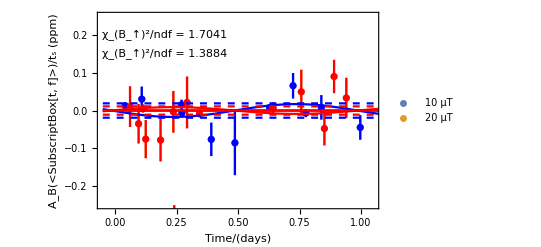

```mathematica
lvl3={};
lvl2={};
tsadd=PlusMinus[11.306,0.397];
sttime=0;
pttstfe10={};fttstfe10={};errtstfe10={};
pttstfet10={};fttstfet10={};errtstfet10={};
pttstfe20={};fttstfe20={};errtstfe20={};
pttstfet20={};fttstfet20={};errtstfet20={};
For[i=1,i≤dimdesc,i++,
lvl2=ReadList[StringJoin[AscDir,seperator,IntegerString[descdat[[i]][[4]],10,6],seperator,IntegerString[descdat[[i]][[4]],10,6],"_lvl2.dat"],metalvl2];
If[i==1,sttime=lvl2[[1]][[1]]];
xx=Mod[((Abs[-lvl2[[1]][[1]]+lvl2[[-1]][[1]]]/2)+Abs[lvl2[[1]][[1]]-sttime])/(24*3600),1];
If[(!MemberQ[{6,7,10},i]&&descdat[[i]][[6]]==10)
,
(*Print["Run 10 #: ",descdat[[i]][[4]]];*)
lvl3=ReadList[StringJoin[AscDir,seperator,IntegerString[descdat[[i]][[4]],10,6],seperator,IntegerString[descdat[[i]][[4]],10,6],"_lvl3.dat"],metalvl3];
ts=(PlusMinus[descdat[[i]][[7]],.1]+tsadd)/PlusMinus[descdat[[i]][[9]],descdat[[i]][[10]]];
(***)
pttstfe10=AppendTo[pttstfe10,{{ts[[1]],ts[[2]]},{lvl3[[1]][[1]],lvl3[[1]][[2]]}*(descdat[[i]][[9]]*10^6/ts[[1]])}];
fttstfe10=AppendTo[fttstfe10,{ts[[1]],lvl3[[1]][[1]]}*(descdat[[i]][[9]]*10^6/ts[[1]])];
errtstfe10=AppendTo[errtstfe10,Sqrt[ts[[2]]^2+lvl3[[1]][[2]]^2]*(descdat[[i]][[9]]*10^6/ts[[1]])];
(***)
pttstfet10=AppendTo[pttstfet10,{xx,{lvl3[[1]][[1]],lvl3[[1]][[2]]}*(descdat[[i]][[9]]*10^6/ts[[1]])}];
fttstfet10=AppendTo[fttstfet10,{xx,lvl3[[1]][[1]]}*(descdat[[i]][[9]]*10^6/ts[[1]])];
errtstfet10=AppendTo[errtstfet10,lvl3[[1]][[2]]*(descdat[[i]][[9]]*10^6/ts[[1]])];
];
If[((MemberQ[{15,17,18,20,22,25,26,27,29,30,31,32,33,35,36},i])&&descdat[[i]][[6]]==20)
,
(*Print["Run 20 #: ",descdat[[i]][[4]]];*)
lvl3=ReadList[StringJoin[AscDir,seperator,IntegerString[descdat[[i]][[4]],10,6],seperator,IntegerString[descdat[[i]][[4]],10,6],"_lvl3.dat"],metalvl3];
ts=(PlusMinus[descdat[[i]][[7]],.1]+tsadd)/PlusMinus[descdat[[i]][[9]],descdat[[i]][[10]]];
(***)
pttstfe20=AppendTo[pttstfe20,{{ts[[1]],ts[[2]]},{lvl3[[1]][[1]],lvl3[[1]][[2]]}*(descdat[[i]][[9]]*10^6/ts[[1]])}];
fttstfe20=AppendTo[fttstfe20,{ts[[1]],lvl3[[1]][[1]]}*(descdat[[i]][[9]]*10^6/ts[[1]])];
errtstfe20=AppendTo[errtstfe20,Sqrt[ts[[2]]^2+lvl3[[1]][[2]]^2]*(descdat[[i]][[9]]*10^6/ts[[1]])];
(***)
pttstfet20=AppendTo[pttstfet20,{xx,{lvl3[[1]][[1]],lvl3[[1]][[2]]}*(descdat[[i]][[9]]*10^6/ts[[1]])}];
fttstfet20=AppendTo[fttstfet20,{xx,lvl3[[1]][[1]]}*(descdat[[i]][[9]]*10^6/ts[[1]])];
errtstfet20=AppendTo[errtstfet20,lvl3[[1]][[2]]*(descdat[[i]][[9]]*10^6/ts[[1]])];
];
]
nlm10=NonlinearModelFit[fttstfet10,m x + c,{m,c},x,Weights->errtstfet10];
ftval10={m/.nlm10["BestFitParameters"],c/.nlm10["BestFitParameters"]};
fterr10=nlm10["ParameterErrors"];
ftresidue10=nlm10["FitResiduals"];
nlm10["ParameterTable"]
nlm10["ANOVATable"]
1+nlm10["EstimatedVariance"]
ndim10=Dimensions[fttstfet10][[1]];
Print["χ2_10: ",(√(∑_(i=1)^ndim10 (pttstfet10[[i]][[2]][[1]]/pttstfet10[[i]][[2]][[2]])^2))/ndim10+1]
(*20*)
nlm20=NonlinearModelFit[fttstfet20,m x + c,{m,c},x,Weights->errtstfet20];
ftval20={m/.nlm20["BestFitParameters"],c/.nlm20["BestFitParameters"]};
fterr20=nlm20["ParameterErrors"];
ftresidue20=nlm20["FitResiduals"];
nlm20["ParameterTable"]
nlm20["ANOVATable"]
1+nlm20["EstimatedVariance"]
ndim20=Dimensions[fttstfet20][[1]];
Print["χ2_20: ",(√(∑_(i=1)^ndim20 (pttstfet20[[i]][[2]][[1]]/pttstfet20[[i]][[2]][[2]])^2))/ndim20]
Show[{
EDAListPlot[pttstfet10,pttstfet20,PlotRange->{{-.05,1.05},{-.25,.25}},PlotLegends->{"10 μT","20 μT"},Frame->True,FrameLabel->{"Time/(days)","A_B(<SubscriptBox[t, f]>)/t_s (ppm)"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->36],LabelStyle->{36,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->{1000},
Epilog->{
Text[Style["χ_(B_↑)^2/ndf = 1.3884",FontSize->Large],{.2,.15}],
Text[Style["χ_(B_↑)^2/ndf = 1.7041",FontSize->Large],{.2,.2}],
Text[Style[
"[A_B(<SubscriptBox[t, f]>)/t_s]_(10  μT): {(-0.017 ± 0.238)Sin[Ωt+(0.085±0.324)] + (-0.000 ± 0.019)}×10^-6\n
[A_B(<SubscriptBox[t, f]>)/t_s]_(20  μT): {(0.009 ± 0.095)Sin[Ωt+(0.085±0.324)] + (-0.000 ± 0.011)}×10^-6
",FontSize->Medium],{.3,-.2}]
}
],
EDAListPlot[pttstfet10,pttstfet20,PlotRange->{{-.05,45},{-.0245,.0245}},Frame->True,FrameLabel->{"Time/(days)","A_B(<SubscriptBox[t, f]>)/t_s (ppm)"},FrameTicks->LinTicks,PlotStyle->{Blue,Red},TicksStyle->Directive[FontSize->36],LabelStyle->{36,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->{1000}
],
Plot[{-.017 Sin[2Pi x+.085],.009Sin[2Pi x+.085]},{x,-.05,45},PlotStyle->{{Thick,Blue},{Thick,Red}}],
Plot[{0,0.019,-0.019,0,0.011,-0.011},{x,-.05,45},PlotStyle->{Blue,{Dashed,Blue},{Dashed,Blue},Red,{Dashed,Red},{Dashed,Red}}]
}]
```